```mathematica
CSVSciensanoHosp = Import[NotebookDirectory[]<>"/sciensano-data/COVID19BE-4.csv",CharacterEncoding->"UTF8"];
CurrentDate=  CSVSciensanoHosp[[2]][[1]];
TotalAmount=0;
day=15;
SciensanoHosp={};
For[i=2,i≤Length[CSVSciensanoHosp],i++,
If[CSVSciensanoHosp[[i]][[1]]==CurrentDate,TotalAmount+=CSVSciensanoHosp[[i]][[5]],SciensanoHosp=Append[SciensanoHosp,{day,TotalAmount}];
day++;
TotalAmount=CSVSciensanoHosp[[i]][[5]];
CurrentDate=CSVSciensanoHosp[[i]][[1]];
];
]
SciensanoHosp=Append[SciensanoHosp,{day,TotalAmount}];
```

```mathematica
CSVSciensanoICU = Import[NotebookDirectory[]<>"/sciensano-data/COVID19BE-4.csv",CharacterEncoding->"UTF8"];
CurrentDate=  CSVSciensanoICU[[2]][[1]];
TotalAmount=0;
day=15;
SciensanoICU={};
For[i=2,i≤Length[CSVSciensanoICU],i++,
If[CSVSciensanoICU[[i]][[1]]==CurrentDate,TotalAmount+=CSVSciensanoICU[[i]][[6]],SciensanoICU=Append[SciensanoICU,{day,TotalAmount}];
day++;
TotalAmount=CSVSciensanoHosp[[i]][[6]];
CurrentDate=CSVSciensanoICU[[i]][[1]]
];
]
SciensanoICU=Append[SciensanoICU,{day,TotalAmount}];
```

```mathematica
CSVSciensanoDea = Import[NotebookDirectory[]<>"sciensano-data/COVID19BE-5.csv",CharacterEncoding->"UTF8"];
CurrentDate=  CSVSciensanoDea[[2]][[1]];
TotalAmount=0;
day=10;
SciensanoDea={};
For[i=2,i≤Length[CSVSciensanoDea],i++,
If[CSVSciensanoDea[[i]][[1]]==CurrentDate,TotalAmount+=CSVSciensanoDea[[i]][[5]],SciensanoDea=Append[SciensanoDea,{day,TotalAmount}];
day++;
TotalAmount=CSVSciensanoDea[[i]][[5]];
CurrentDate=CSVSciensanoDea[[i]][[1]]
];
]
SciensanoDea=Append[SciensanoDea,{day,TotalAmount}];
SciensanoDeaCumul={{10,SciensanoDea[[1]][[2]]}};
For[i=2,i≤ Length[SciensanoDea],i++,
SciensanoDeaCumul=Append[SciensanoDeaCumul,{i+9, SciensanoDeaCumul[[i-1]][[2]]+SciensanoDea[[i]][[2]]}];
]
```

```mathematica
(* NEW version 7 -> 19/04/2020 *)

(* nombre cumulé de cas positifs *)
dataBe = {{1, 1}, {2, 2}, {3, 8}, {4, 13}, {5, 25}, {6, 50}, {7,
    109}, {8, 313}, {9, 340}, {10, 404}, {11, 498}, {12, 597}, {13,
    767}, {14, 1014}, {15, 1352}, {16, 1529}, {17, 1744}, {18,
    2132}, {19, 2550}, {20, 3086}, {21, 3802}, {22, 4465}, {23,
    4935}, {24, 5424}, {25, 6754}, {26, 7948}, {27, 9147}, {28,
    10508}, {29, 12027}, {30, 12872}, {31, 13555}, {32, 15295}, {33,
    16975}, {34, 18481}, {35, 19927}, {36, 21616}, {37, 22534}, {38,
    23169}, {39, 25039}, {40, 26469}, {41, 27839}, {42, 29119}, {43,
    29583}, {44, 29587}, {45, 30589}, {46, 31}};
    
(* nombre de patients hospîtalisés CONSOLIDATED *)
datahosp = {{1, 0}, {2, 0}, {3, 0}, {4, 0}, {5, 0}, {6, 0}, {7,
    0}, {8, 0}, {9, 0}, {10, 0}, {11, 0}, {12, 0}, {13, 0}, {14,
    27}, {15, 97}, {16, 163}, {17, 265}, {18, 368}, {19, 496}, {20,
    649}, {21, 842}, {22, 1097}, {23, 1381}, {24, 1644}, {25,
    1881}, {26, 2138}, {27, 2718}, {28, 3072}, {29, 3644}, {30,
    4081}, {31, 4474}, {32, 4886}, {33, 4979}, {34, 5210}, {35,
    5362}, {36, 5497}, {37, 5514}, {38, 5606}, {39, 5744}, {40,
    5699}, {41, 5597}, {42, 5618}, {43, 5645}, {44, 5419}, {45,
    5423}, {46, 5536}, {47, 5515}, {48, 5309}, {49, 5161}, {50,
    5069}, {51, 4871}, {52, 4920}, {53, 4976}};
datahosp = Join[Take[datahosp,14], SciensanoHosp];
    
(* nombre de patients en soins intensifs (ICU) CONSOLIDATED *)
datalits = {{1, 0}, {2, 0}, {3, 0}, {4, 0}, {5, 0}, {6, 0}, {7,
    0}, {8, 0}, {9, 0}, {10, 0}, {11, 0}, {12, 0}, {13, 2}, {14,
    15}, {15, 24}, {16, 33}, {17, 53}, {18, 79}, {19, 100}, {20,
    130}, {21, 164}, {22, 238}, {23, 290}, {24, 322}, {25, 381}, {26,
    474}, {27, 605}, {28, 690}, {29, 789}, {30, 867}, {31, 927}, {32,
    1021}, {33, 1088}, {34, 1144}, {35, 1205}, {36, 1245}, {37,
    1261}, {38, 1267}, {39, 1260}, {40, 1276}, {41, 1285}, {42,
    1278}, {43, 1262}, {44, 1232}, {45, 1234}, {46, 1226}, {47,
    1204}, {48, 1182}, {49, 1140}, {50, 1119}, {51, 1081}, {52,
    1071}, {53, 1079}};
datalits = Join[Take[datalits,14], SciensanoICU];
    
(* décès cumulés *)
datamort = {{1, 0}, {2, 0}, {3, 0}, {4, 0}, {5, 0}, {6, 0}, {7,
    0}, {8, 0}, {9, 0}, {10, 0}, {11, 0}, {12, 3}, {13, 3}, {14,
    3}, {15, 3}, {16, 4}, {17, 10}, {18, 10}, {19, 14}, {20, 21}, {21,
     37}, {22, 67}, {23, 75}, {24, 88}, {25, 122}, {26, 178}, {27,
    220}, {28, 289}, {29, 353}, {30, 431}, {31, 513}, {32, 705}, {33,
    828}, {34, 1011}, {35, 1143}, {36, 1283}, {37, 1447}, {38,
    1632}, {39, 2035}, {40, 2240}, {41, 2523}, {42, 3019}, {43,
    3346}, {44, 3600}, {45, 3903}, {46, 4157}, {47, 4440}, {48,
    4857}, {49, 5163}, {50, 5453}, {51, 5683}, {52, 5828}, {53,
    5828 + 170}};
datamort = Join[Take[datamort,9], SciensanoDeaCumul];
    
(* décès journaliers CONSOLIDATED *)
ddatamort = {{1, 0}, {2, 0}, {3, 0}, {4, 0}, {5, 0}, {6, 0}, {7,
    0}, {8, 0}, {9, 0}, {10, 0}, {11, 0}, {12, 0}, {13, 1}, {14,
    3}, {15, 3}, {16, 5}, {17, 5}, {18, 10}, {19, 10}, {20, 19}, {21,
    25}, {22, 27}, {23, 36}, {24, 46}, {25, 75}, {26, 69}, {27,
    91}, {28, 91}, {29, 115}, {30, 128}, {31, 133}, {32, 158}, {33,
    172}, {34, 238}, {35, 193}, {36, 224}, {37, 269}, {38, 225}, {39,
    267}, {40, 299}, {41, 321}, {42, 275}, {43, 323}, {44, 283}, {45,
    338}, {46, 270}, {47, 262}, {48, 266}, {49, 240}, {50, 191}, {51,
    98}, {52, 22}};
ddatamort = Join[Take[ddatamort,9], SciensanoDea];
    
(* données hebdo sciensano = second pic de grippe à comparer avec \
incidence par 100.000 *)
datagrippe = {{13, 200}, {20, 405}, {27, 741}, {34, 581}, {41,
    498}, {48, 224}};
(* percentage morts H / morts TOTAL *)
fracmortsH = (2655)/(5828);
(*---------------------------------------------------------------------------------------------------*)
(* PARAMETRES FIXES *)

jour = Length[datahosp];
Window = 8;
hh = 0.05;             (* fraction d'hospitalisés *)

gamma = 1/12.4;  (* INVERSE RECOVERY TIME *)

epsilon = 1./5.2; (* INVERSE INCUBATION TIME  *)

dea = 0.50;               (* mortalité en ICU *)

alpha = 0.15/10;  (* DEATH RATE INMR/MRS *)

n0 = 11000000;   (* Population initiale x proportion susceptible d'être infectée *)

n0MRS = 400000;  (* Population en MR/MRS + personnel soignant *)

(*---------------------------------------------------------------------------------------------------\
*)
(* POUR PRENDRE LES DATA AU VOL LORS DE LA CONF DE PRESSE  *)

datamort2 = {};
s = 0;
For[day = 1, day <= Length[ddatamort], day++,
  s = s + ddatamort[[day]][[2]];
  datamort2 = Join[datamort2, {{day, s}}];
  ];
datamort = datamort2;

(*---------------------------------------------------------------------------------------------------\
*)
```

```mathematica
listr0 = {};
For[day = 1, day <= Length[datahosp] + 60, day++,
  listr0 = Join[listr0, {{day, 4.3}}];
  ];

SEIR[dday_] := (
   drea = dea*1/5;
   rrea = (1 - dea)*1/20;
   n = n0;
   i = i0;
   e = i*37;
   h = 0.0;
   l = 0.0;
   r = 0.0;
   m = 0.0;
   s = n - e - i - r;
   hospi = 0.0;
   cost = 0.0;
   cost2 = 0.0;
   For[day = 1, day <= dday, day++,
    lambda = (gamma+hospi)*listr0[[day]][[2]];
    (*lambda = gamma*listr0[[day]][[2]];*)
    If[day == 15, hospi = hh/7;];
    ds = -lambda*(i/2 + e)*s/n;                  (*
    infection by exposed (contagiousness) and half infected (self-
    isolation) *)
    de = lambda*(i/2 + e)*s/n - epsilon*e;
    di = epsilon*e - gamma*i - hospi*i;
    dh = hospi*i - gg*h/7 - (1 - gg)*h/(4 + 2 Tanh[(l - 500)/300]);
    dl = (1 - gg)*h/(4 + 2 Tanh[(l - 500)/300]) - drea*l - rrea*l;
    dr = gamma*i + rrea*l + gg*h/7;
    dm = drea*l;
    s += ds;
    e += de;
    i += di;
    h += dh;
    l += dl;
    If[l > 1895, dm = dm + (l - 1895); l = 1895.0;];
    r += dr;
    m += dm;
    n = s + e + i + h + l + r;
    If[day <= Length[datahosp],
     cost = cost + (l + h - datahosp[[day]][[2]])^2;];
    If[day <= Length[datahosp],
     cost2 =
       cost2 + (l + h - datahosp[[day]][[2]])^2 + (l -
           datalits[[day]][[2]])^2;];
    ];
   cost2 =
    cost2 + (m - fracmortsH* datamort[[Length[datamort]]][[2]])^2;
   Return[{s, e, i, h, l, m, r, cost, cost2}];
   );

(* FIT DES CONDITIONS INITIALES SUR LES PREMIERES DONNEES > i0 *)

besti0 = 3;
i0 = 3;
gg = 0.75;
bestcost = SEIR[25][[8]];
For[k = 1, k <= 50, k = k + 0.3,
  i0 = k;
  temp = SEIR[25];
  If[temp[[8]] < bestcost, bestcost = temp[[8]]; besti0 = k;];
  ];

i0 = besti0;
Print["i0=", i0];

(* Fit of Hosp data + ICU + Pourcentage *)

bestcost2 = SEIR[Length[datahosp]][[9]]*20;
bestgg = gg;
```

i0=31.

```mathematica
For[kgg = 0.65, kgg < 0.85, kgg = kgg + 0.03,
  gg = kgg;
  For[da = 10, da <= Length[datahosp] - Window, da++,
   bestr0 = listr0[[da]][[2]];
   bestcost = SEIR[da + Window][[9]];
   For[k = 0.3, k <= 5.0, k = k + 0.05,
    For[j = 0, j <= Length[listr0] - da, j++,
     listr0[[da + j]][[2]] = k;];
    temp = SEIR[da + Window];
    If[temp[[9]] < bestcost, bestcost = temp[[9]]; bestr0 = k; ];
    ];
   For[j = 0, j <= Length[listr0] - da, j++,
    listr0[[da + j]][[2]] = bestr0;];
   ];
  temp = SEIR[Length[datahosp]];
  If[temp[[9]] < bestcost2,
   bestcost2 = temp[[9]];
   bestgg = kgg;
   bestlistr0 = listr0;];
  ];

Print["gg=", bestgg];
gg = bestgg;

listr0 = bestlistr0;
dataMRS = {};
For[k = 1, k <= Length[datamort], k++,
  dataMRS = Join[dataMRS, {{k, datamort[[k]][[2]] - SEIR[k][[6]]}}];
  ];

(*-------------- FIT R0 DES MRS ------------*)

listr0MRS = {};
For[day = 1, day <= Length[datahosp] + 60, day++,
  listr0MRS = Join[listr0MRS, {{day, 4.3}}];
  ];
```

gg=0.83

```mathematica
SEIRMRS[dday_] := (
   alpha = 0.15/10;
   lambda = gamma*4.3;
   n = n0MRS;
   i = 1;
   e = i*20;
   r = 0.0;
   s = n - e - i - r;
   m = 0.0;
   cost = 0.0;
   For[day = 1, day <= dday, day++,
    lambda = gamma*listr0MRS[[day]][[2]];
    ds = -lambda*(i/2 + e)*s/n;                 
    de = lambda*(i/2 + e)*s/n - (epsilon)*e;
    di = epsilon*e - (gamma + alpha)*i;
    dr = gamma*i;
    dm = alpha*i;
    s += ds;
    e += de;
    i += di;
    r += dr;
    m += dm;
    n = s + e + i + r;
    If[day <= Length[dataMRS],
     cost = cost + (m - dataMRS[[day]][[2]])^2; ];
    ];
   Return[{s, e, i, m, r, cost}];
   );

For[da = Window, da <= Length[dataMRS] - Window, da++,
  bestr0 = listr0MRS[[da]][[2]];
  bestcost = SEIRMRS[da + Window][[6]];
  For[k = 0.3, k <= 6.3, k = k + 0.2,
   For[j = 0, j <= Length[listr0MRS] - da, j++,
    listr0MRS[[da + j]][[2]] = k;];
   temp = SEIRMRS[da + Window];
   If[temp[[6]] < bestcost, bestcost = temp[[6]]; bestr0 = k; ];
   ];
  For[j = 0, j <= Length[listr0MRS] - da, j++,
   listr0MRS[[da + j]][[2]] = bestr0;];
  ];
```

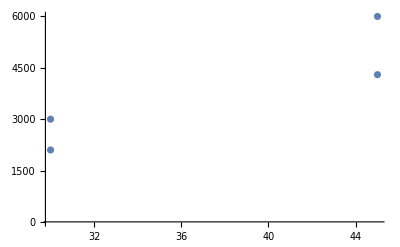

```mathematica
listc = {};
listi = {};
listh = {};
listl = {};
listm = {};
listm2 = {};
For[da = 1, da <= Length[datahosp] + 60, da++,
  temp = SEIR[da];
  temp2 = SEIRMRS[da];
  listc =
   Join[listc, {{da, (temp[[3]] + temp[[4]] + temp[[5]] + temp[[6]] +
          temp[[7]])/n0*100000}}];
  listi = Join[listi, {{da, temp[[3]]/n0*100000}}];
  listh = Join[listh, {{da, temp[[4]] + temp[[5]]}}];
  listl = Join[listl, {{da, temp[[5]]}}];
  listm = Join[listm, {{da, temp[[6]] + temp2[[4]]}}];
  listm2 = Join[listm2, {{da, temp[[6]]}}];
  ];

(* graphes *)

serologicalTests= ListPlot[{{30,2100},{45,4300},{30,3000},{45,6000}}]

lits0 = ListPlot[{listh, listl, listm, listm2}, Joined -> True,
   PlotRange -> All, PlotStyle -> {Blue, Red, Black, Gray},
   Frame -> True,
   FrameLabel -> {"Days since first infection", "Number"},
   LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 13, Black},
   FrameStyle -> Directive[Thickness[0.002], 13],
   Filling -> {1 -> {2}, 2 -> Bottom, 3 -> 4, 4 -> Bottom}];

model = ListPlot[{listc, listi}, Joined -> {True, True, False},
   PlotRange -> All,
   PlotStyle -> {ColorData["HTML"]["DarkOliveGreen"],
     ColorData["HTML"]["YellowGreen"],
     Directive[Black, PointSize[Large]]}, Frame -> True,
   FrameLabel -> {"Days since first infection", "Number"},
   LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 13, Black},
   FrameStyle -> Directive[Thickness[0.002], 13],
   Filling -> {1 -> Bottom, 2 -> Bottom, None}, AspectRatio -> 1/4];

plotBe = ListPlot[dataBe, PlotStyle -> Black];

plotlits =
  ListPlot[{datahosp, datalits, datamort},
   PlotStyle -> {Directive[Blue, PointSize[Large]],
     Directive[Red, PointSize[Large]],
     Directive[Black, PointSize[Large]]}];

plotr0 = ListPlot[{listr0, listr0MRS}, Joined -> True,
   PlotRange -> All, PlotStyle -> {Orange, Brown}, Frame -> True,
   FrameLabel -> {"Days since first infection", "Re"},
   LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 13, Black},
   Filling -> 0, FrameStyle -> Directive[Thickness[0.002], 13],
   AspectRatio -> 1/8, Axes -> False];
```

```mathematica
plotcaption =
  Graphics[{{Dashed, Line[{{jour, 0}, {jour, 10000}}]},
    Text[Style["Incidence per 100.000", Medium], {20.0, 6000},
     Automatic]}];
     
plotcaption3 =
  Graphics[{{Dashed, Line[{{jour - Window, 0}, {jour - Window, 10000}}]},
    Text[Style["Incidence per 100.000", Medium], {20.0, 6000},
     Automatic]}];

plotcaption2 =
  Graphics[{Text[
     Style["ICU capacity", Medium,
      ColorData["HTML"]["FireBrick"]], {16, 2150}, Automatic],
    Text[Style[
      "Belgium - May 22 \n SEIR model @vdwnico \n \
______________________", Medium], {20.5, 9000}, Automatic]}];

plottoday =
  Graphics[{{Dashed, Line[{{jour, 0}, {jour, 25000}}]},
    Text[Style["Today", Medium], {jour - .5, 6650},
     Automatic, {0, 1}]}];
     
plotwindow =
  Graphics[{{Dashed, Line[{{jour- Window, 0}, {jour - Window, 25000}}]},
    Text[Style["Window", Medium], {jour - Window - .5, 6650},
     Automatic, {0, 1}]}];

plotzone =
  Plot[{1895 + 0 x, 1950 + 0 x}, {x, -10, 180}, Filling -> {1 -> {2}},
    PlotStyle -> {ColorData["HTML"]["FireBrick"],
     ColorData["HTML"]["FireBrick"], {ColorData["HTML"]["FireBrick"],
      Opacity[0.5]}}];

plotlegend = Graphics[{
    Text[Style["• in hospitals", Medium,
      Blue], {10, 7500}, {Left, Center}],
    Text[Style["• in ICU", Medium, Red], {10,
      7000}, {Left, Center}],
    Text[Style["• total deaths", Medium,
      Black], {10, 6500}, {Left, Center}],
    Text[Style["- deaths in Hosp", Medium, Gray], {10, 6000}, {Left,
      Center}]}];

plotlegend2 = Graphics[{
    Text[Style["- total cases", Medium,
      ColorData["HTML"]["DarkOliveGreen"]], {11, 5000}, {Left,
      Center}],
    Text[Style["- active cases", Medium,
      ColorData["HTML"]["YellowGreen"]], {11, 4200}, {Left, Center}]}];

plotlegend3 = Graphics[{
    Text[Style["- in population", Medium, Orange], {35, 4}, {Left,
      Center}],
    Text[Style["- in MR/MRS", Medium, Brown], {35, 3}, {Left,
      Center}]}];

If[listr0[[-1]][[2]]<0.8,R0Color=RGBColor[0.3,0.7,0.3],If[listr0[[-1]][[2]]>1.2,R0Color=RGBColor[0.7,0.3,0.3],R0Color=RGBColor[0.9,0.7,0.3]]];
plotFinalR0 = Graphics[{Text[Style[listr0[[-1]][[2]], FontSize->16,R0Color],{jour+3,3},{Left,Center}]}];
```

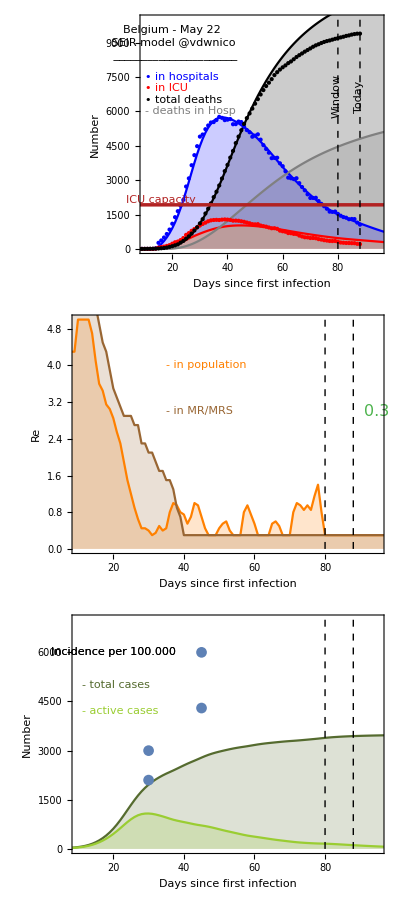

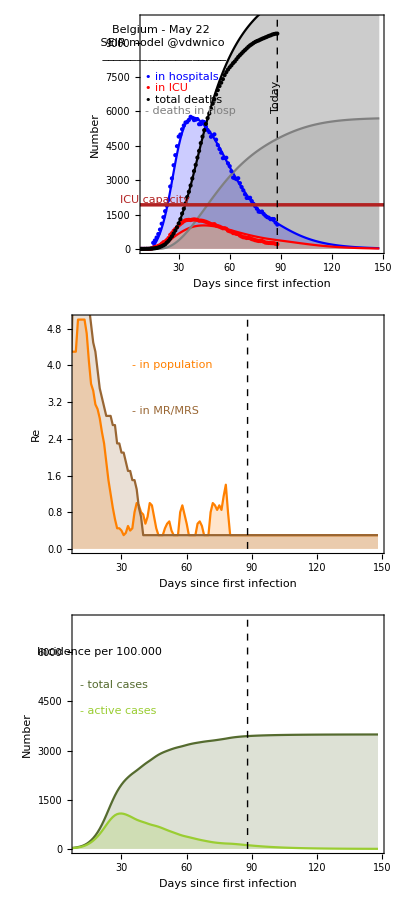

```mathematica
final = Multicolumn[{Show[lits0, plotlits, plotzone, plottoday, plotwindow,
    plotlegend, plotcaption2, PlotRange -> {{10, jour + 7}, {0, 10000}},
    ImageSize -> 600, ImagePadding -> {{70, 2}, {0, 1}}],
   Show[{plotr0, plotFinalR0, plotlegend3,
     Graphics[{Dashed, Line[{{jour - Window, 0}, {jour - Window, 25}}]}],Graphics[{Dashed, Line[{{jour, 0}, {jour, 25}}]}]},
    PlotRange -> {{10, jour + 7}, {0, 5}}, ImageSize -> 600,
    ImagePadding -> {{70, 2}, {2, 2}}],
   Show[{model, plotlegend2, plotcaption,plotcaption3, serologicalTests},
    PlotRange -> {{10, jour + 7}, {0, 7000}}, ImageSize -> 600,
    ImagePadding -> {{70, 2}, {40, 1}}]
   }, 1]
   
finalFuture = Multicolumn[{Show[lits0, plotlits, plotzone, plottoday,
    plotlegend, plotcaption2, PlotRange -> {{10, jour+60}, {0, 10000}},
    ImageSize -> 600, ImagePadding -> {{70, 2}, {0, 1}}],
   Show[{plotr0, plotlegend3,
     Graphics[{Dashed, Line[{{jour, 0}, {jour, 25}}]}]},
    PlotRange -> {{10, jour+60}, {0, 5}}, ImageSize -> 600,
    ImagePadding -> {{70, 2}, {2, 2}}],
   Show[{model, plotlegend2, plotcaption},
    PlotRange -> {{10, jour+60}, {0, 7000}}, ImageSize -> 600,
    ImagePadding -> {{70, 2}, {40, 1}}]
   }, 1]
```

```mathematica
Export[NotebookDirectory[]<>"/results/SEIR-belgium-"<> DateString[{"ISODate"}] <> ".pdf", final, ImageResolution -> 600];
```